# 11.1A Homework

## Problem 1:

```mathematica
(*List the first five terms of the sequence.*)
```

```mathematica
Subscript[a, n]= (-1)^(n-1)/6^n;
```

```mathematica
Subscript[a, 1]= 1/6
```

```mathematica
Subscript[a, 2]= -1/36
```

```mathematica
Subscript[a, 3]= 1/6^3
```

1/216

```mathematica
Subscript[a, 4]= -1/6^4
```

-1/1296

```mathematica
Subscript[a, 5]= 1/6^5
```

1/7776

## Problem 2:

```mathematica
(*Find a formula for the general term an of the sequence,assuming that the pattern of the first few terms continues.(Assume that n begins with 1.) *)
```

```mathematica
{1/1,1/3,1/5,1/7,1/9,...}
```

```mathematica
(*Used video help; exact same question*)
```

```mathematica
Subscript[a, n]= 1/(2n-1)
```

## Problem 3:

```mathematica
{3,7,11,15,19,...}
```

```mathematica
(*Arithmatic Sequence*)
(*GENERAL FORMULA*) Subscript[a, n]=Subscript[a, 1]+theDiffBtInt(n-1);
```

```mathematica
Subscript[a, n]= 3+4(n-1);
```

## Problem 4:

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[n_]:= 1+ (-2/5)^n;
```

```mathematica
For[i=1,i⩽10,i++,Print[N[F[i]]]]
```

0.6

1.16

0.936

1.0256

0.98976

1.0041

0.998362

1.00066

0.999738

1.0001

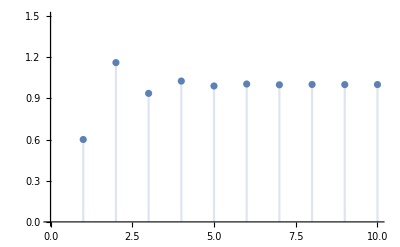

```mathematica
DiscretePlot[F[n],{n,0,10}]
```

```mathematica
Limit[F[n],n-> ∞]
```

1

## Problem 5:

```mathematica
(*Determine whether the sequence converges or diverges.If it converges,find the limit.(If an answer does not exist,enter DNE.)*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[n_]:=6-(1/2)^n;
```

```mathematica
Limit[F[n],n-> ∞]
```

6

## Problem 6:

```mathematica
(*Determine whether the sequence converges or diverges.If it converges,find the limit.(If an answer does not exist,enter DNE.)*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[n_]:=n^3/(8n+4);
```

```mathematica
Limit[F[n],n-> ∞]
```

∞